```mathematica
Clear[Oz]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
FI[n_]:=FactorInteger[n];FI[1]:={}
oz[n_,z_]:=Product[z^p[[2]],{p,FI[n]}]
ooz[n_,z_]:=Product[z^p[[2]]/p[[2]]!,{p,FI[n]}]
Oz[n_,z_]:=Oz[n,z]=Sum[oz[j,z],{j,1,n}]
Oz2[n_,k_]:=Sum[(-1)^(k-j)bin[k,j]Oz[n,j],{j,0,20}]
dOz2[n_,k_]:=Oz2[n,k]-Oz2[n-1,k]
Ozz[n_,z_]:=Sum[bin[z,k]Oz2[n,k],{k,0,Log2@n}]
LOz[n_,k_]:=D[Oz[n,z],{z,k}]/.z->0
dLOz[n_,k_]:=LOz[n,k]-LOz[n-1,k]
Ozzz[n_,z_]:=Sum[z^k/k! LOz[n,k],{k,0,Log2@n}]
roots[n_]:=If[(c=Exponent[f=Oz[n,z],z])==0,{},If[c==1,List@NRoots[f==0,z][[2]],List@@NRoots[f==0,z][[All,2]]]]
rroots[n_]:=If[(c=Exponent[f=Oz[n,z],z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
```

```mathematica
Table[Oz2[100,n],{n,1,10}]//TableForm
```

99
612
2244
4368
4080
1440
0
0
0
0

```mathematica
Expand@Oz[100,z]
```

1+25 z+34 z^2+22 z^3+12 z^4+4 z^5+2 z^6

```mathematica
Ozz[100,1]
```

100

```mathematica
Table[dLoz[n,k],{n,1,20},{k,0,10}]//Grid
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 24 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
roots[30]
```

{-2.21592,-0.586297-1.29619 ⅈ,-0.586297+1.29619 ⅈ,-0.111491}

```mathematica
rr[n_]:=Chop@FullSimplify@Sum[-rho^-1,{rho,roots[n]}]
```

```mathematica
rr[100]
```

25.

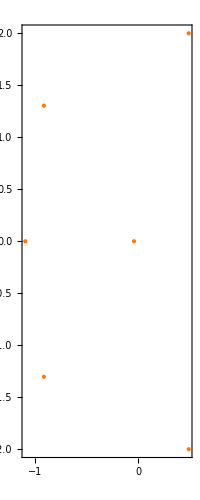

```mathematica
Graphics[Table[{ColorData["RustTones"][n/100],Point[{Re[#],Im[#]}]}&/@roots[n],{n,100,100}],Frame->True]
```

```mathematica
Expand@Sum[Binomial[z,k](x)^(z-k),{k,0,Infinity}]
```

(1+1/x)^z x^z